```mathematica
NonTermName[nonterm_]:=ReplaceAll[nonterm,NonTerm[x_]:>x];
NonTermWithProd[nonterm_,prodIndex_]:=NonTerm[NonTermName[nonterm],prodIndex];

ApplyGrammarProduction[root_,index_,prodRuleIndex_,grammar_]:=Block[{rootNonTerm,newLeafs,edgeList,vertexLabels},
rootNonTerm = NonTermWithProd[root,prodRuleIndex];
newLeafs = grammar[[prodRuleIndex]]["To"];
edgeList = Thread[index->Range[index+1,index+Length[newLeafs]]];
vertexLabels = Prepend[Thread[Range[index+1,index+Length[newLeafs]]->newLeafs],index->rootNonTerm];
{Graph[edgeList,VertexLabels->vertexLabels],vertexLabels}
];
```

```mathematica
root = NonTerm["cond"];
```

```mathematica
compatibleProductions = Select[grammar,#["From"]==NonTermName[root]&]
```

{<|From→cond,To→{Term[logicOp],NonTerm[cond],NonTerm[cond]},Value→Term[logicOp][Value][NonTerm[cond][Value],NonTerm[cond][Value]]|>,<|From→cond,To→{Term[not],NonTerm[cond]},Value→!NonTerm[cond][Value]|>,<|From→cond,To→{Term[numOp],NonTerm[numQuant],NonTerm[numQuant]},Value→Term[numOp][Value][NonTerm[numQuant][Value],NonTerm[numQuant][Value]]|>}

```mathematica
selectedProdRule = RandomChoice[compatibleProductions]
```

<|From→cond,To→{Term[numOp],NonTerm[numQuant],NonTerm[numQuant]},Value→Term[numOp][Value][NonTerm[numQuant][Value],NonTerm[numQuant][Value]]|>

```mathematica
prodRuleIndex = First@FirstPosition[grammar,selectedProdRule]
```

3

```mathematica
rootNonTerm = NonTermWithProd[root,prodRuleIndex]
```

NonTerm[cond,3]

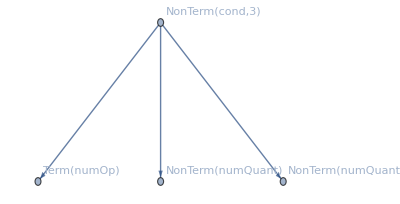
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp],3→NonTerm[numQuant],4→NonTerm[numQuant]}}

```mathematica
ApplyGrammarProduction[NonTerm["cond"],1,3,grammar]
```